# 3D Rashba, D+p-wave SC

## Hamiltonian

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
ξ[kx_,ky_,kz_]:=-μ-2t1(Cos[kx]+Cos[ky])-4t2 Cos[kx]Cos[ky]-2tz Cos[kz]
g[kx_,ky_,kz_]:=α1{-Sin[ky],Sin[kx],0}+α2{0,0,Sin[kx]Sin[ky]Sin[kz](Cos[kx]-Cos[ky])}
HN[kx_,ky_,kz_]:=ξ[kx,ky,kz]σ0+g[kx,ky,kz].{σ1,σ2,σ3}
ψ[kx_,ky_,kz_]:=Δd(Cos[kx]-Cos[ky])
d[kx_,ky_,kz_]:=Δp{Sin[ky],Sin[kx],0}
Δ[kx_,ky_,kz_]:=(ψ[kx,ky,kz]σ0+d[kx,ky,kz].{σ1,σ2,σ3}).(ⅈ σ2)
```

```mathematica
HBdG[kx_,ky_,kz_,qx_,qy_,qz_]:={{HN[kx+qx,ky+qy,kz+qz],Δ[kx,ky,kz]},{Δ[kx,ky,kz]†,-Transpose[HN[-kx+qx,-ky+qy,-kz+qz]]}}//ArrayFlatten
```

## Bogoliubov quasiparticle energy spectrum

```mathematica
params=<|t1->1,t2->0.2,tz->0.5,μ->-0.7,α1->0.3,α2->0.3,Δd->0.5,Δp->0.2|>;
viewpoint={1.0979209015572695,-3.1573045999459657,0.5253545061039633};
SetDirectory[NotebookDirectory[]];
```

### Main figures

```mathematica
Module[{temp1,temp2,plot},
Do[
temp1=PrintTemporary["k_z=",kz];
Do[
temp2=PrintTemporary["q=",q];
plot=Plot3D[
{Sort[Eigenvalues[HBdG[kx,ky,kz,q[[1]],q[[2]],q[[3]]]/.params],Greater][[1;;2]],
Sort[Eigenvalues[HBdG[kx,ky,kz,q[[1]],q[[2]],q[[3]]]/.params],Greater][[3;;4]]},
{kx,-π,π},{ky,-π,π},
PlotRange->{-0.4,0.4},MaxRecursion->10,ViewPoint->viewpoint,
ImageSize->Large,Mesh->None,ClippingStyle->None,BoxRatios->{1, 1, 0.4},
PlotStyle->{{Orange,Opacity[0.7]},{Lighter[Blue],Opacity[0.7]}},
Ticks->{{-π,0,π},{-π,0,π},{-0.4,0,0.4}},TicksStyle->20,
AxesLabel->{
Text[Style["k_x",FontFamily->"Times New Roman",Italic,FontSize->30]],
Text[Style["k_y",FontFamily->"Times New Roman",Italic,FontSize->30]],
Text[Style["E",FontFamily->"Times New Roman",Italic,FontSize->30]]
}
];
Export["images_mathematica/spectrum_kz"<>ToString[N[kz]]<>"_qx"<>ToString[q[[1]]]<>"_qy"<>ToString[q[[2]]]<>"_qz"<>ToString[q[[3]]]<>".png",plot];
NotebookDelete[temp2],
{q,{0.1{1/(√2),0,1/(√2)}}}(*{{0,0,0},0.1{1,0,0},0.1{1/(√2),1/(√2),0},0.1{1/(√2),0,1/(√2)},0.1{0,0,1}}*)
];
NotebookDelete[temp1],
{kz,{0,π/2,π}}]
]
```

```mathematica
paramsα2zero=params;
paramsα2zero[α2]=0;
Module[{plot},
plot=Plot3D[
{Sort[Eigenvalues[HBdG[kx,ky,π/2,0.1,0,0]/.paramsα2zero],Greater][[1;;2]],
Sort[Eigenvalues[HBdG[kx,ky,π/2,0.1,0,0]/.paramsα2zero],Greater][[3;;4]]},
{kx,-π,π},{ky,-π,π},
PlotRange->{-0.4,0.4},MaxRecursion->10,ViewPoint->viewpoint,
ImageSize->Large,Mesh->None,ClippingStyle->None,BoxRatios->{1, 1, 0.4},
PlotStyle->{{Orange,Opacity[0.7]},{Lighter[Blue],Opacity[0.7]}},
Ticks->{{-π,0,π},{-π,0,π},{-0.4,0,0.4}},TicksStyle->20,
AxesLabel->{
Text[Style["k_x",FontFamily->"Times New Roman",Italic,FontSize->30]],
Text[Style["k_y",FontFamily->"Times New Roman",Italic,FontSize->30]],
Text[Style["E",FontFamily->"Times New Roman",Italic,FontSize->30]]
}
];
Export["images_mathematica/spectrum_a2zero_kz"<>ToString[N[π/2]]<>"_qx0.1_qy0_qz0.png",plot]
]
```

images_mathematica/spectrum_a2zero_kz1.5708_qx0.1_qy0_qz0.png

```mathematica
Module[{temp,q,shift,plot},
q=0.8;
Do[
temp=PrintTemporary["k_z=",kzv];
shift=(Grad[ξ[kx,ky,kz],{kx,ky,kz}].{q/(√2),0,q/(√2)})/.Join[params,<|kx->π/2,ky->π/2,kz->kzv|>]-0.05;
plot=Plot3D[
{Sort[Eigenvalues[HBdG[kx,ky,kzv,q/(√2),0,q/(√2)]/.params],Greater][[1;;2]],
Sort[Eigenvalues[HBdG[kx,ky,kzv,q/(√2),0,q/(√2)]/.params],Greater][[3;;4]]},
{kx,π/3,2π/3},{ky,π/3,2π/3},
PlotRange->{shift-0.05,shift+0.05},MaxRecursion->15,ViewPoint->viewpoint,
ImageSize->Large,Mesh->None,ClippingStyle->None,BoxRatios->{1, 1, 0.4},
PlotStyle->{{Orange,Opacity[0.7]},{Lighter[Blue],Opacity[0.7]}},
Ticks->{{π/3,2π/3},{π/3,2π/3},Automatic},TicksStyle->20,
AxesLabel->{
Text[Style["k_x",FontFamily->"Times New Roman",Italic,FontSize->30]],
Text[Style["k_y",FontFamily->"Times New Roman",Italic,FontSize->30]],
Text[Style["E",FontFamily->"Times New Roman",Italic,FontSize->30]]
}
];
Export["images_mathematica/spectrum_kz"<>ToString[kzv]<>"_qx"<>ToString[q/(√2)]<>"_qy0.0_qz"<>ToString[q/(√2)]<>".png",plot];
NotebookDelete[temp],
{kzv,{-0.02,0,0.05}}
];
]
```

### Animations

```mathematica
plots1=Table[
Plot3D[
Sort[Eigenvalues[HBdG[kx,ky,0,q,0,0]/.params],Greater],{kx,-π,π},{ky,-π,π},
PlotLabel->Text[Style["q="<>ToString[q],FontFamily->"Times",Italic,FontSize->30]],
AxesLabel->{Text[Style["k_x",FontFamily->"Times",Italic,FontSize->30]],Text[Style["k_y",FontFamily->"Times",Italic,FontSize->30]],Text[Style["E",FontFamily->"Times",Italic,FontSize->30]]},
ImageSize->Large,ViewPoint->viewpoint,
PlotRange->{-1.1,1.1},MaxRecursion->10,
ClippingStyle->None,BoxRatios->{1, 1, 0.6},TicksStyle->20
],
{q,0,0.3,0.05}
];
```

```mathematica
plots2=Table[
Plot3D[
Sort[Eigenvalues[HBdG[kx,ky,π/2,q,0,0]/.params],Greater],{kx,-π,π},{ky,-π,π},
PlotLabel->Text[Style["q="<>ToString[q],FontFamily->"Times",Italic,FontSize->30]],
AxesLabel->{Text[Style["k_x",FontFamily->"Times",Italic,FontSize->30]],Text[Style["k_y",FontFamily->"Times",Italic,FontSize->30]],Text[Style["E",FontFamily->"Times",Italic,FontSize->30]]},
ImageSize->Large,ViewPoint->viewpoint,
PlotRange->{-1.1,1.1},MaxRecursion->10,
ClippingStyle->None,BoxRatios->{1, 1, 0.6},TicksStyle->20
],
{q,0,0.3,0.05}
];
```

```mathematica
plots3=Table[
Plot3D[
Sort[Eigenvalues[HBdG[kx,ky,π,q,0,0]/.params],Greater],{kx,-π,π},{ky,-π,π},
PlotLabel->Text[Style["q="<>ToString[q],FontFamily->"Times",Italic,FontSize->30]],
AxesLabel->{Text[Style["k_x",FontFamily->"Times",Italic,FontSize->30]],Text[Style["k_y",FontFamily->"Times",Italic,FontSize->30]],Text[Style["E",FontFamily->"Times",Italic,FontSize->30]]},
ImageSize->Large,ViewPoint->viewpoint,
PlotRange->{-1.1,1.1},MaxRecursion->10,
ClippingStyle->None,BoxRatios->{1, 1, 0.6},TicksStyle->20
],
{q,0,0.3,0.05}
];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["images_mathematica/spectrum1.gif",plots1]
```

images_mathematica/spectrum1.gif

```mathematica
Export["images_mathematica/spectrum2.gif",plots2]
```

images_mathematica/spectrum2.gif

```mathematica
Export["images_mathematica/spectrum3.gif",plots3]
```

images_mathematica/spectrum3.gif

## Fermi surfaces and nodes

```mathematica
viewpoint={0.7263902855272396,-2.962025713532005,1.4658652139493908};
params=<|t1->1,t2->0.2,tz->0.5,μ->-0.7,α1->0.3,α2->0.3,Δd->0.5,Δp->0.2|>;
SetDirectory[NotebookDirectory[]];
```

```mathematica
ENp[kx_,ky_,kz_]:=ξ[kx,ky,kz]+Norm[g[kx,ky,kz]]
ENm[kx_,ky_,kz_]:=ξ[kx,ky,kz]-Norm[g[kx,ky,kz]]
```

```mathematica
fs=ContourPlot3D[
(*{Sort[Eigenvalues[HN[kx,ky,kz]/.params],Greater][[1]]==0,
Sort[Eigenvalues[HN[kx,ky,kz]/.params],Greater][[2]]==0}*)
{(ENp[kx,ky,kz]/.params)==0,(ENm[kx,ky,kz]/.params)==0},
{kx,-π,π},{ky,-π,π},{kz,0,π},
ViewPoint->viewpoint,BoundaryStyle->None,
ImageSize->Large,Mesh->None,BoxRatios->{1, 1, 0.5},
ContourStyle->{{Orange,Opacity[0.3]},{Lighter[Blue],Opacity[0.3]}},
Ticks->{{},{},{0,π}},TicksStyle->30,
AxesLabel->{
Text[Style["k_x",FontFamily->"Times New Roman",Italic,FontSize->40]],
Text[Style["k_y",FontFamily->"Times New Roman",Italic,FontSize->40]],
Text[Style["k_z",FontFamily->"Times New Roman",Italic,FontSize->40]]
}
];
```

```mathematica
lines=Graphics3D[
{Dashed,Black,Line[Table[{{-π,(-1)^n π,π Floor[(n-1)/2]},{π,(-1)^(n-1)π,π Floor[(n-1)/2]}},{n,4}]]}
];
```

### Line nodes

```mathematica
lnodesol1={kx,ky,kz}/.Solve[{(ENp[kx,kx,kz]/.params)==0,kx==Abs[ky]},{ky,kz}];
lnodesol2={kx,ky,kz}/.Solve[{(ENm[kx,kx,kz]/.params)==0,kx==Abs[ky]},{ky,kz}];
```

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

```mathematica
lnodes1=ParametricPlot3D[Evaluate@lnodesol1,{kx,-π,π},PlotStyle->Directive[Red,Thickness[0.015]]];
lnodes2=ParametricPlot3D[Evaluate@lnodesol2,{kx,-π,π},PlotStyle->Directive[Red,Thickness[0.015]]];
```

```mathematica
plotl=Show[fs,lines,lnodes1,lnodes2];
Export["images_mathematica/fermi_surface_line_nodes.png",plotl]
```

images_mathematica/fermi_surface_line_nodes.png

### Point nodes

```mathematica
pnodesol1=Flatten[{{kx,kx,0},{kx,-kx,0}}/.Solve[{(ENp[kx,kx,0]/.params)==0},{kx}],1];
pnodesol2=Flatten[{{kx,kx,0},{kx,-kx,0}}/.Solve[{(ENm[kx,kx,0]/.params)==0},{kx}],1];pnodesol3=Flatten[{{kx,kx,π},{kx,-kx,π}}/.Solve[{(ENp[kx,kx,π]/.params)==0},{kx}],1];
pnodesol4=Flatten[{{kx,kx,π},{kx,-kx,π}}/.Solve[{(ENm[kx,kx,π]/.params)==0},{kx}],1];
```

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

```mathematica
pnodes1=Graphics3D[{Red,Sphere[pnodesol1,0.1]}];
pnodes2=Graphics3D[{Red,Sphere[pnodesol2,0.1]}];
pnodes3=Graphics3D[{Red,Sphere[pnodesol3,0.1]}];
pnodes4=Graphics3D[{Red,Sphere[pnodesol4,0.1]}];
```

```mathematica
plotp=Show[fs,lines,pnodes1,pnodes2,pnodes3,pnodes4];
Export["images_mathematica/fermi_surface_point_nodes.png",plotp]
```

images_mathematica/fermi_surface_point_nodes.png

## Chern number

```mathematica
params=<|t1->1,t2->0.2,tz->0.5,μ->-0.7,α1->0.3,α2->0.3,Δd->0.5,Δp->0.2|>;
SetDirectory[NotebookDirectory[]];
```

### Sign of g_q'.(g×d)

```mathematica
gdiff[qx_,qy_,qz_,kx_,ky_,kz_]:=Grad[g[x,y,z],{x,y,z}].{qx,qy,qz}/.{x->kx,y->ky,z->kz}
gu[kx_,ky_,kz_]:=g[kx,ky,kz]/Norm[g[kx,ky,kz]]
Simplify[-gdiff[qx,qy,qz,kx,kx,kz].(g[kx,kx,kz]×d[kx,kx,kz])]
Simplify[-gdiff[qx,qy,qz,kx,-kx,kz].(g[kx,-kx,kz]×d[kx,-kx,kz])]
```

2 (-qx+qy) α1 α2 Δp Sin[kx]^5 Sin[kz]

-2 (qx+qy) α1 α2 Δp Sin[kx]^5 Sin[kz]

```mathematica
Module[{reg,fs,plot},
Do[
fs=ContourPlot[
{((ξ[varkx,ky,kz]+Norm[g[varkx,ky,kz]])/.params)==0,
((ξ[varkx,ky,kz]-Norm[g[varkx,ky,kz]])/.params)==0},
{ky,-π,π},{kz,-π,π},
ContourStyle->{{Thickness[0.01],Orange,Dashed},{Thickness[0.01],Orange,Dashed}}
(*FrameTicks->{{{-π,0,π},None},{{-π,0,π},None}},FrameTicksStyle->30,
FrameLabel->{
Text[Style["k_y",FontFamily->"Times New Roman",Italic,FontSize->40]],
Text[Style["k_z",FontFamily->"Times New Roman",Italic,FontSize->40]]
}*)
];
reg=RegionPlot[
Sign[Cos[varkx]-Cos[ky]]>0,{ky,-π,π},{kz,-π,π},
BoundaryStyle->None,PlotStyle->LightGray,
ImageSize->Medium,FrameTicks->None
];
plot=Show[reg,fs];
Export["images_mathematica/fermi_surface_kx"<>ToString[N[varkx]]<>".png",plot],
{varkx,{1.0,1.2,1.4,1.6,1.8}}
]
]
```

### k_(||) vector plot

```mathematica
ep[kx_,ky_,kz_]:=ξ[kx,ky,kz]+Norm[g[kx,ky,kz]]
em[kx_,ky_,kz_]:=ξ[kx,ky,kz]-Norm[g[kx,ky,kz]]
kperp[kx_,ky_,kz_]:=Normalize[
{DifferenceQuotient[(ep[x,y,z]/.params),{x,10^-6}],
DifferenceQuotient[(ep[x,y,z]/.params),{y,10^-6}],
DifferenceQuotient[(ep[x,y,z]/.params),{z,10^-6}]}
]/.{x->kx,y->ky,z->kz}
kparax[kx_,ky_,kz_]:={1,0,0}×kperp[kx,ky,kz]
kparay[kx_,ky_,kz_]:={0,1,0}×kperp[kx,ky,kz]
```

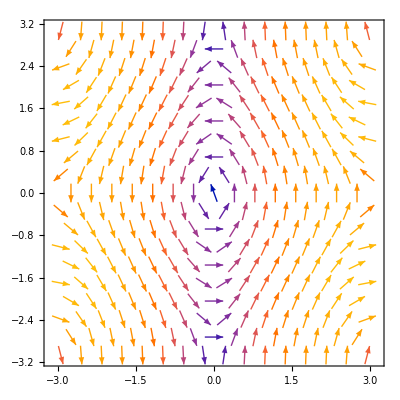

```mathematica
vecx[ky_,kz_]:=kparax[1.5,ky,kz][[2;;3]]
VectorPlot[vecx[ky,kz],{ky,-π,π},{kz,-π,π}]
```

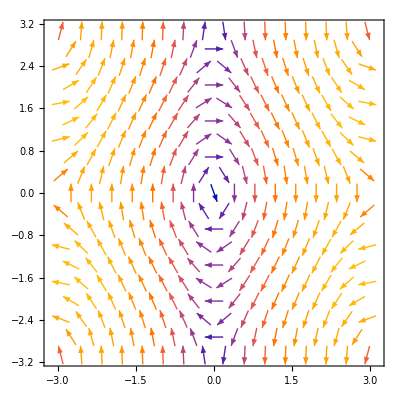

```mathematica
vecy[kx_,kz_]:=kparay[kx,1.5,kz][[{1,3}]]
VectorPlot[vecy[kx,kz],{kx,-π,π},{kz,-π,π}]
```

## Symmetry argument

```mathematica
e=<|"k"->IdentityMatrix[3],"BdG"->IdentityMatrix[4]|>;
c4z=<|"k"->RotationMatrix[π/2,{0,0,1}],"BdG"->ArrayFlatten[{{MatrixExp[-ⅈ π/4 σ3],0},{0,-MatrixExp[-ⅈ π/4 σ3]*}}]|>;
c2z=<|"k"->RotationMatrix[π,{0,0,1}],"BdG"->ArrayFlatten[{{MatrixExp[-ⅈ π/2 σ3],0},{0,MatrixExp[-ⅈ π/2 σ3]*}}]|>;
c4zi=<|"k"->RotationMatrix[-π/2,{0,0,1}],"BdG"->ArrayFlatten[{{MatrixExp[ⅈ π/4 σ3],0},{0,-MatrixExp[ⅈ π/4 σ3]*}}]|>;
mx=<|"k"->-RotationMatrix[π,{1,0,0}],"BdG"->ArrayFlatten[{{MatrixExp[-ⅈ π/2 σ1],0},{0,MatrixExp[-ⅈ π/2 σ1]*}}]|>;
my=<|"k"->-RotationMatrix[π,{0,1,0}],"BdG"->ArrayFlatten[{{MatrixExp[-ⅈ π/2 σ2],0},{0,MatrixExp[-ⅈ π/2 σ2]*}}]|>;
mxy1=<|"k"->-RotationMatrix[π,{1,1,0}],"BdG"->ArrayFlatten[{{MatrixExp[-ⅈ π/(2 √2)(σ1+σ2)],0},{0,-MatrixExp[-ⅈ π/(2 √2)(σ1+σ2)]*}}]|>;
mxy2=<|"k"->-RotationMatrix[π,{1,-1,0}],"BdG"->ArrayFlatten[{{MatrixExp[-ⅈ π/(2 √2)(σ1-σ2)],0},{0,-MatrixExp[-ⅈ π/(2 √2)(σ1-σ2)]*}}]|>;
trs=<|"k"->-IdentityMatrix[3],"BdG"->KroneckerProduct[σ0,-ⅈ σ2]|>;
phs=<|"k"->-IdentityMatrix[3],"BdG"->KroneckerProduct[σ1,σ0]|>;
cs=<|"k"->IdentityMatrix[3],"BdG"->KroneckerProduct[σ1,σ2]|>;
```

```mathematica
preservedsym[qx,qy,qz]:=Module[{cond,sym,preservedu,preservedt,preservedp,preservedc,kx,ky,kz},
cond={t1∈Reals,t2∈Reals,tz∈Reals,μ∈Reals,α1∈Reals,α2∈Reals,Δd∈Reals,Δp∈Reals,kx∈Reals,ky∈Reals,kz∈Reals};
sym={"e","c4z","c2z","c4zi","mx","my","mxy1","mxy2"};
preservedu=Select[sym,
FullSimplify[
Symbol[#]["BdG"].HBdG[kx,ky,kz,qx,qy,qz].Symbol[#]["BdG"]†
-Apply[HBdG,{Symbol[#]["k"].{kx,ky,kz},qx,qy,qz}//Flatten],
cond]==ConstantArray[0,{4,4}]&
];
preservedt=StringInsert[Select[sym,
FullSimplify[
Symbol[#]["BdG"].trs["BdG"].HBdG[kx,ky,kz,qx,qy,qz]*.trs["BdG"]†.Symbol[#]["BdG"]†
-Apply[HBdG,{Symbol[#]["k"].trs["k"].{kx,ky,kz},qx,qy,qz}//Flatten],
cond]==ConstantArray[0,{4,4}]&
],
"t×",1
];
preservedp=StringInsert[Select[sym,
FullSimplify[
Symbol[#]["BdG"].phs["BdG"].HBdG[kx,ky,kz,qx,qy,qz]*.phs["BdG"]†.Symbol[#]["BdG"]†
+Apply[HBdG,{Symbol[#]["k"].phs["k"].{kx,ky,kz},qx,qy,qz}//Flatten],
cond]==ConstantArray[0,{4,4}]&
],
"p×",1
];
preservedc=StringInsert[Select[sym,
FullSimplify[
Symbol[#]["BdG"].cs["BdG"].HBdG[kx,ky,kz,qx,qy,qz].cs["BdG"]†.Symbol[#]["BdG"]†
+Apply[HBdG,{Symbol[#]["k"].cs["k"].{kx,ky,kz},qx,qy,qz}//Flatten],
cond]==ConstantArray[0,{4,4}]&
],
"c×",1
];
Join[preservedu,preservedt,preservedp,preservedc]
]
```

```mathematica
preservedsym[0.,0.,0.]
```

{e,c4z,c2z,c4zi,mx,my,mxy1,mxy2,t×e,t×c4z,t×c2z,t×c4zi,t×mx,t×my,t×mxy1,t×mxy2,p×e,p×c4z,p×c2z,p×c4zi,p×mx,p×my,p×mxy1,p×mxy2,c×e,c×c4z,c×c2z,c×c4zi,c×mx,c×my,c×mxy1,c×mxy2}

```mathematica
preservedsym[1.,0.,0.]
```

{e,my,t×c2z,t×mx,p×e,p×my,c×c2z,c×mx}

```mathematica
preservedsym[0.,1.,0.]
```

{e,mx,t×c2z,t×my,p×e,p×mx,c×c2z,c×my}

```mathematica
preservedsym[1.,1.,0.]
```

{e,mxy2,t×c2z,t×mxy1,p×e,p×mxy2,c×c2z,c×mxy1}

```mathematica
preservedsym[1.,2.,0.]
```

{e,t×c2z,p×e,c×c2z}